# Analytical solutions for simple cases

First let us assume is small i.e.,  
and using geometric series expansion . 
We also assume that 
 
as a quadratic geometry. Thus the resulting ODE is:

The ODE is of the form: 
where 
 
.
The solution is

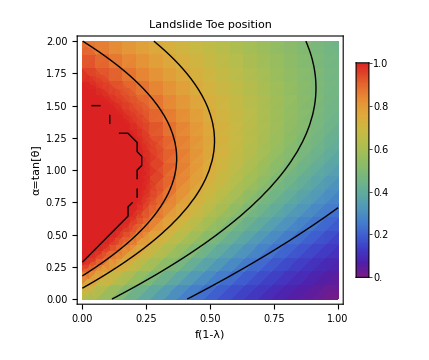

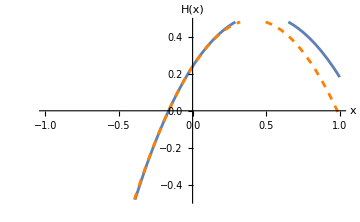
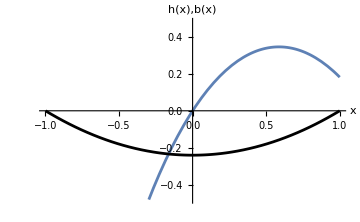

```mathematica
(*Define parameters as symbolic*)
ClearAll[H,H0,x,α](*α -> Tan[θ]*)
P[x_]:=Subscript[b, 0] (α-2 Subscript[b, 0] x (1+α^2))
Q[x_]:=-Subscript[f, λ]+α-4 Subscript[b, 0] x (1+α^2)
(*Solve the ODE symbolically*)
solH=DSolve[{H'[x]+P[x] H[x]==Q[x],H[0]==H0},H[x],{x,-1,1}];
Hanalytical = H[x]/.solH[[1]];

(*Define H[x]*)
HBC = 0.24;
bmax=HBC;
αplot = 1.3;
fplot=0.0;
Happroxfun[x_,fv_?NumericQ,αv_?NumericQ]:=HBC+(αv-(fv+bmax*HBC*αv))*x+(bmax*x^2)/2*(fv*αv-(4+5*αv^2));
Hfun[x_,fv_,αv_]:=Evaluate[Hanalytical/.{x->x,Subscript[f, λ]->fv,α->αv,Subscript[b, 0]->bmax,H0->HBC}];

(*Function to return positive root or 1 if none exists*)
xPosRoot[fv_?NumericQ,αv_?NumericQ]:=Module[{roots},roots=x/. NSolve[Hfun[x,fv,αv]==0&&0<=x<=1,x,Reals];
If[roots==={}||!VectorQ[roots,NumericQ],1,Min[roots]]];

dplot=DensityPlot[xPosRoot[fv,αv],{fv,0,1},{αv,0,2},ColorFunction->ColorData[{"Rainbow",{0,1}}],FrameLabel->{"f(1-λ)","α=tan[θ]"},PlotLabel->"Landslide Toe position",PlotPoints->20,Mesh->False,PlotLegends->BarLegend[{"Rainbow",{0,1}}],ImageSize->Medium,LabelStyle->{FontSize->15}
];
cplot = ContourPlot[xPosRoot[fv,αv],{fv,0,1},{αv,0,2},Contours->{0.1,0.2,0.4,0.6,0.8,0.9,1.0},ContourStyle->Black,ContourShading->None
];
fig=Show[dplot,cplot]
(*Export[NotebookDirectory[]<>"LandslideToeParameterPlot.jpg",fig,"JPEG"]*)
(*Plot one H-x profile*)
Row[{
Plot[{Hfun[x,fplot,αplot],Happroxfun[x,fplot,αplot]},{x,-1,1},PlotRange->{-2*bmax,2*HBC},AxesLabel->{"x","H(x)"},LabelStyle->{FontSize->13},PlotStyle->{DarkBlue,{Orange,Dashed}},ImageSize->Medium],
Spacer[20],
Plot[{Hfun[x,fplot,αplot]+bmax*(x^2-1),bmax*(x^2-1)},{x,-1,1},PlotRange->{-2*bmax,2*HBC},AxesLabel->{"x","h(x),b(x)"},LabelStyle->{FontSize->13},PlotStyle->{DarkBlue,Black},ImageSize->Medium]
}]
```

```mathematica
(*bmaxList={0.01,0.05,0.1,0.2,0.4,0.8};
colorMap=ColorData["ThermometerColors"];  (*Or "Rainbow","Viridis",etc.*)
colors=colorMap/@Rescale[Range[Length[bmaxList]]];  (*Evenly spaced colors*)
Plot[Evaluate@Table[bmax*(x^2-1),{bmax,bmaxList}],{x,-1,1},PlotStyle->(Directive[#,Thick]&/@colors),PlotLegends->Placed[LineLegend[Style[#,FontSize->12]&/@ToString/@bmaxList,LegendLabel->Style["b-max",FontSize->14]],Right],AxesLabel->{"x","b(x)"},LabelStyle->{FontSize->14},PlotLabel->Style["Profiles of b(x)",FontSize->16],ImageSize->Large]*)
```

Abs[b_0]-2 b_0-(5 α^2 b_0)/2-f_λ+α (1-Abs[b_0] b_0+(b_0 f_λ)/2)

(2-2 Abs[b_0] b_0+b_0 f_λ-2 √(10 b_0 (Abs[b_0]-2 b_0-f_λ)+(1-Abs[b_0] b_0+(b_0 f_λ)/2)^2))/(10 b_0)

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

(2-2 Abs[b_0] b_0+b_0 f_λ+2 √(10 b_0 (Abs[b_0]-2 b_0-f_λ)+(1-Abs[b_0] b_0+(b_0 f_λ)/2)^2))/(10 b_0)

Power::infy: Infinite expression 1/0. encountered.

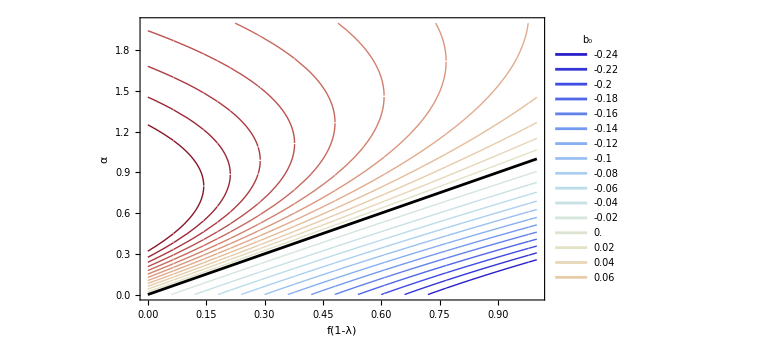

/Users/mallick/Documents/GitHub/landslides/analyticsol/LandslideToeStabilityBoundaryPlot.jpg

```mathematica
Hlocus[x_]:=Abs[Subscript[b, 0]]+(α-(Subscript[f, λ]+Subscript[b, 0] Abs[Subscript[b, 0]]*α))*x+(Subscript[b, 0]*x^2)/2*(Subscript[f, λ]*α-(4+5*α^2));
(*Hlocus[x_]:=Evaluate[Hanalytical/.H0->Subscript[b, 0]]*)
Collect[Hlocus[1],{α^2,α}]
locus=Solve[Hlocus[1]==0,α,Assumptions->{1>=Subscript[f, λ]>=0}];
locussol = α/. locus[[1]]
locusfun[f_,b_]:=Evaluate[locussol/.{Subscript[f, λ]->f,Subscript[b, 0]->b}]
bvals=Range[-0.24,0.24,0.02];
colorMap=ColorData["ThermometerColors"];
colors=colorMap/@Rescale[Range[Length[bvals]]];  (*Evenly spaced colors*)
p1=Plot[Evaluate@Table[locusfun[f,b],{b,bvals}],{f,0,1},PlotStyle->(Directive[#,Thick]&/@colors),PlotLegends->Placed[LineLegend[Style[#,FontSize->15]&/@ToString/@bvals,LegendLabel->Style[Subscript[b,0],FontSize->15]],Right],ImageSize->Large,PlotRange->{0,2}];
locussol = α/. locus[[2]]
locusfun[f_,b_]:=Evaluate[locussol/.{Subscript[f, λ]->f,Subscript[b, 0]->b}]
p2=Plot[Evaluate@Table[locusfun[f,b],{b,bvals}],{f,0,1},PlotStyle->(Directive[#,Thick]&/@colors),ImageSize->Large,PlotRange->{0,2}];
p3=Plot[f,{f,0,1},PlotStyle->{Black}];
fig=Show[p1,p2,p3,FrameLabel->{"f(1-λ)","α"},Frame->True,LabelStyle->{FontSize->18}]
Export[NotebookDirectory[]<>"LandslideToeStabilityBoundaryPlot.jpg",fig,"JPEG"]
```

## Function to solve the true ODE and find the stability boundary

```mathematica
(*Define function to find 'x' where H=0 for given α,f,b0*)
xPosRoot[αv_?NumericQ,fv_?NumericQ, b0_?NumericQ]:=Module[{sol,res},sol=Quiet@Check[NDSolve[{-D[H[x],x] - 0.5*(αv-2 b0 x)/(1+(2 b0 x)^2)*2 b0/(1+2 b0 x*αv)*H[x] == fv+2 b0 x -(αv-2 b0 x)/(1+2 b0 x*αv),H[0]==Abs[b0]},H,{x,0,1}],$Failed];
If[sol===$Failed,10,(*fallback if solve fails*)
Quiet@Check[res=x/.Last[FindRoot[((H[x]/. sol)==0),{x,0.9,0,1}]],10]
]
]
```

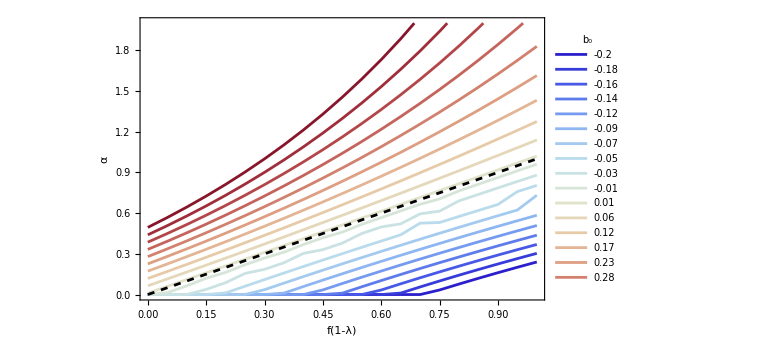

```mathematica
locusfun[f_,b0_]:=Module[{res},res=Quiet@FindRoot[xPosRoot[α,f,b0]==1.0,{α,0.0,0,3}];
α/. res]

(*bvals={-0.2,-0.1,-0.05,-0.02,-0.01,0.01,0.05,0.1,0.2,0.4};*)
bvals=Join[Subdivide[-0.2,-0.01,9],Subdivide[0.01,0.5,9]];
roundedLabels = Round[bvals,0.01];
fvals=Range[0,1,0.05];  

(*Parallel computation of {f,alpha} pairs for each b value*)
data=ParallelTable[{f,locusfun[f,b]},{b,bvals},{f,fvals}];

(*Plot each set of points as a line*)
p1=ListLinePlot[data,PlotRange->{0,2},PlotLegends->Placed[LineLegend[roundedLabels,LegendLabel->Style["b₀",Bold,18]],Right],LabelStyle->{FontSize->18},ImageSize->Large,PlotStyle->ColorData["ThermometerColors"]/@Rescale[Range[Length[bvals]]]];
p2=Plot[f,{f,0,1},PlotStyle->{Black,Dashed}];
fig=Show[p1,p2,FrameLabel->{"f(1-λ)","α"},Frame->True,LabelStyle->{FontSize->18}]
(*Export[NotebookDirectory[]<>"LandslideToeTrueStabilityBoundaryPlot.jpg",fig,"JPEG"]*)
```

## Create figure for landslide toe position and various topographic profiles (ice-free case)

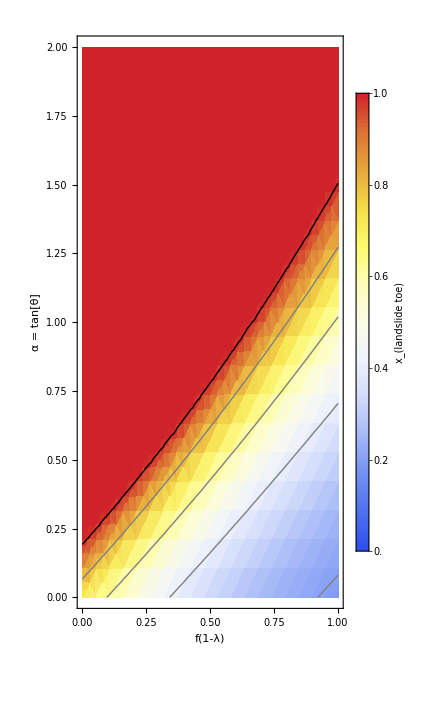

/Users/mallickrishg/Documents/GitHub/landslides/analyticsol/LandslideToeParameterPlot.jpg

```mathematica
(*Define function to find 'x' where H=0 for given α,f,b0*)
xPosRoot[αv_?NumericQ,fv_?NumericQ, b0_?NumericQ]:=Module[{sol,res},sol=Quiet@Check[NDSolve[{-D[H[x],x] - 0.5*(αv-2 b0 x)/(1+(2 b0 x)^2)*2 b0/(1+2 b0 x*αv)*H[x] == fv+2 b0 x -(αv-2 b0 x)/(1+2 b0 x*αv),H[0]==Abs[b0]},H,{x,0,1}],$Failed];
If[sol===$Failed,1.0,(*fallback if solve fails*)
Quiet@Check[res=x/.Last[FindRoot[((H[x]/. sol)==0),{x,0.9,0,1}]],1.01]
]
]
bplotval = 0.2;
contours={0,0.2,0.4,0.6,0.8,0.99};
(*legend=BarLegend["Temperature",LegendMarkers->Automatic,LegendLabel->Style[Subscript[x,"landslide toe"],FontSize->14],
LabelStyle->Directive[FontSize->14],LegendLayout->"Vertical",LegendMarkers->Table[If[v==0.99,Style[v,Bold,14],v],{v,contours}]];*)

dplot=DensityPlot[
Clip[xPosRoot[αv,fv,bplotval],{0,1.02}],(*clamp values to[0,1]*){fv,0,1},{αv,0,2},ColorFunction->(ColorData[{"Temperature",{0,1}}][#]&),ColorFunctionScaling->False,(*use actual values,not rescaled*)FrameLabel->{"f(1-λ)","α = tan[θ]"},PlotPoints->20,Mesh->False,PlotLegends->BarLegend[{ColorData[{"Temperature",{0,1}}],{0,1}},LegendLabel->Style[Subscript[x,"landslide toe"],FontSize->14]],ImageSize->Medium,LabelStyle->{FontSize->15}];

cplot=ContourPlot[xPosRoot[αv,fv,bplotval],{fv,0,1},{αv,0,2},Contours->contours,ContourStyle->{Gray,Gray,Gray,Gray,Gray,Directive[Black,Thick]},ContourShading->None];

fig=Show[dplot,cplot,AspectRatio->2]
Export[NotebookDirectory[]<>"LandslideToeParameterPlot.jpg",fig,"JPEG",ImageResolution->500]
```

InterpolatingFunction::dmval: Input value {-0.999959} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: Exp[-2.32721×10^36] is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {-0.999959} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: Exp[-2.15382×10^38] is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {-0.999959} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::munfl: Exp[-6.33116×10^38] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

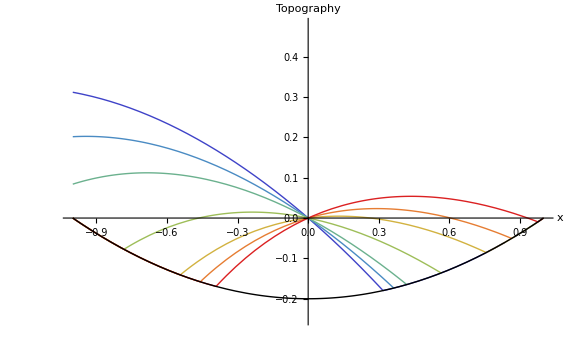

/Users/mallickrishg/Documents/GitHub/landslides/analyticsol/LandslideToeTopographicProfiles.jpg

```mathematica
fvval = 0.6;
paramSets={
{0.1,fvval,bplotval},
{0.2,fvval,bplotval},
{0.3,fvval,bplotval},
{0.5,fvval,bplotval},
{0.7,fvval,bplotval},
{0.8,fvval,bplotval},
{0.9,fvval,bplotval}};
(*Number of parameter sets*)
nlines=Length[paramSets];

Hsol[αv_?NumericQ,fv_?NumericQ,b0_?NumericQ]:=
Quiet@Module[{bv,sollogss,φ},
(*Define the profile bv[x] here if needed*)
bv[x_]:=b0*(x^2-1);
(*Solve the modified ODE for Φ[x]*)sollogss=Quiet@NDSolve[{-Exp[φ[x]]*φ'[x]-0.5*(αv-bv'[x])/(1+(bv'[x])^2)*bv''[x]/(1+bv'[x]*αv)*Exp[φ[x]]==fv+bv'[x]-(αv-bv'[x])/(1+bv'[x]*αv),φ[0]==Log[Abs[b0]]},φ,{x,-1,1}];
(*Return H[x]=Exp[Φ[x]] as an interpolating function*)
Function[x,Exp[φ[x]/. sollogss[[1]]]]];

(*Generate a list of H[x]+b[x] and b[x] curves for each parameter set*)
curves = Table[Module[{Hf,αv,fv,b0,color},{αv,fv,b0}=
paramSets[[i]];
Hf=Hsol[αv,fv,b0];
color=ColorData["Rainbow"][i/nlines];(*gradient from blue to red*)
{Style[Hf[x]+bplotval*(x^2-1),color,Thick]}  (*dashed baseline*)],{i,nlines}];

(*Flatten the list so all curves are in a single list*)
curvesFlat=Flatten[curves,1];

(*Plot all curves together*)
fig=Plot[Evaluate[Join[curvesFlat,{Style[bplotval*(x^2-1),Black,Thick]}]],{x,-1,1},
PlotRange->{-1.25*bplotval,2.4*bplotval},PlotLegends->None,Frame->None,AxesLabel->{"x","Topography"},LabelStyle->{FontSize->20},ImageSize->Large]
Export[NotebookDirectory[]<>"LandslideToeTopographicProfiles.jpg",fig,"JPEG"]
```

## Similar exercise as before for case with ice buttress